```mathematica
Clear["Global`*"]
```

```mathematica
AA0=t0 vn^2;
AA2=1+8 eta;
AA4=-9 (eta+4 eta^2);
```

```mathematica
C2= t0 vn^2/(√(1+2 eta))
```

(t0 vn^2)/(√(1+2 eta))

```mathematica
C0=(1+2 eta)^(3/2)*(1+6 eta) t0 vn^2
```

(1+2 eta)^(3/2) (1+6 eta) t0 vn^2

```mathematica
BB2=Simplify[(AA0^2 (AA2^2-2 AA4)+C2^2+2 AA0 (AA4 C0-AA2 C2))/((AA0-C0) (AA0 AA2-C2))]
```

(1+34 eta+136 eta^2+1/(1+2 eta)-(2 (1+17 eta+126 eta^2+612 eta^3+1224 eta^4+864 eta^5))/(√(1+2 eta)))/((1+8 eta-1/(√(1+2 eta))) (1-(1+2 eta)^(3/2) (1+6 eta)))

```mathematica
PP2=Simplify[-(2 AA0 AA4)/(AA0 AA2-C2)+(AA0 AA2-C2)/(AA0-C0)]
```

(18 eta (1+4 eta))/(1+8 eta-1/(√(1+2 eta)))+(1+8 eta-1/(√(1+2 eta)))/(1-(1+2 eta)^(3/2) (1+6 eta))

```mathematica
BB4=Simplify[((AA0 AA2-C2)/(AA0-C0))^2]
```

(-1-8 eta+1/(√(1+2 eta)))^2/((-1+(1+2 eta)^(3/2) (1+6 eta))^2)

```mathematica
RUp=Simplify[(1+8 eta-1/(√(1+2 eta)))*√(1+2 eta)]
```

-1+√(1+2 eta)+8 eta √(1+2 eta)

```mathematica
RDn=Simplify[(1-(1+2 eta)^(3/2) (1+6 eta))*√(1+2 eta)]
```

√(1+2 eta) (1-(1+2 eta)^(3/2) (1+6 eta))

```mathematica
Series[PP2,{eta,0,3}]
```

1+(32 eta)/3-(32 eta^2)/9+(170 eta^3)/27+O[eta]^4

```mathematica
Series[BB4,{eta,0,3}]
```

1-(14 eta)/3+(128 eta^2)/9-(958 eta^3)/27+O[eta]^4

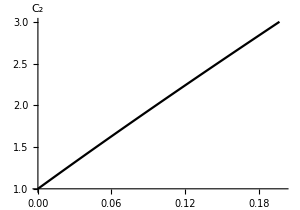
-Graphics-η

```mathematica
Labeled[Plot[PP2,{eta,0,0.2},PlotStyle->{Directive[Black,Thick]},PlotRange->{{0,0.2},{1,3}},AxesLabel->{Style["",FontSize->20],Style[Text@TraditionalForm@Style[Subscript[C, 2],20,Bold]]},AspectRatio->0.7,ImageSize->300],Text@TraditionalForm@Style[η,20,Bold]]
```

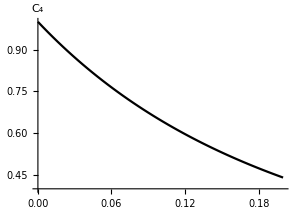
-Graphics-η

```mathematica
Labeled[Plot[BB4,{eta,0,0.2},PlotStyle->{Directive[Black,Thick]},PlotRange->{{0,0.2},{0.4,1}},AxesLabel->{Style["",FontSize->20],Style[Text@TraditionalForm@Style[Subscript[C, 4],20,Bold]]},AspectRatio->0.7,ImageSize->300],Text@TraditionalForm@Style[η,20,Bold]]
```